For UCSD, S14 Physics 161
Reference: http://www.maplesoft.com/applications/view.aspx?SID=4240&view=html

```mathematica
Clear["Global`*"]
```

START OF CONFIG: Edit parameters in this section to your preference.

```mathematica
(*Mass of black hole.*)
mBlackHole:=1
(*Mass of object.*)
mObject:=1

(*Initial radial coordinate.*)
r0:=50
(*Initial rate of change of the radial coordinate wrt proper distance.*)
dr0:=0

(*Initial azimuthal coordinate.*)
φ0:=Pi/4
(*Initial rate of change of azimuthal coordinate wrt proper distance.*)
dφ0:=0

(*This many increments of proper distance.*)
steps:=1000
```

Constants (in natural units for simplicity)

```mathematica
G:=1(*gravitational constant*)
c:=1(*speed of light*)
rs:=2*G*mBlackHole/c^2 (*schwarzschild radius of black hole*)
```

END OF CONFIG: Changing code below may alter script behavior.

Schwarzschild metric geodesics.

```mathematica
angularMomentum:=dφ0*r0^2*mObject
energy:=mObject*c*Sqrt[dr0^2+(1-rs/r0)*(c^2+(angularMomentum/r0/mObject)^2)]
```

Radial Euler-Lagrange equation

```mathematica
rEq:=r''[s]/(1-rs/r[s])-rs/2/(r[s]-rs)^2*(r'[s]^2-(c*energy)^2)-angularMomentum^2/r[s]^3==0
```

Azimuthal Euler-Lagrange equation

```mathematica
φEq:=φ'[s]==angularMomentum/r[s]^2/mObject
```

Initial conditions

```mathematica
init:={r[0]==r0, r'[0]==dr0, φ[0]==φ0}
```

Solving the equations

```mathematica
(*
NDSolve is a numerical differential equation solver.
1st arg (Join[{rEq, φEq}, init]) is a list of the necessary differential equations and initial conditions.
2nd arg ({r[s], φ[s]}) is the list of functions NDSolve is solving for.
3rd arg ({s, 0, steps}) is the range of values NDSolve will enumerate using the calculated r[s] and φ[s].
4th arg Method->{"EventLocator","Event":>r[s]-rs,"EventAction":>Throw[steps=s,"StopIntegration"]}
			is a condition set on NDSolve to put an upper limit on how many steps it can take.
			NDSolve is set to stop calculating when it reaches the Schwarzschild radius, namely, when r[s]-rs=0.
*)
sol=NDSolve[
Join[{rEq, φEq}, init],
{r[s], φ[s]},
{s,0, steps},
Method->{"EventLocator","Event":>r[s]-rs,
"EventAction":>Throw[steps=s,"StopIntegration"]}
]
```

{{r[s]→InterpolatingFunction[{{0., 391.349}}, <>][s],φ[s]→InterpolatingFunction[{{0., 391.349}}, <>][s]}}

Static plot

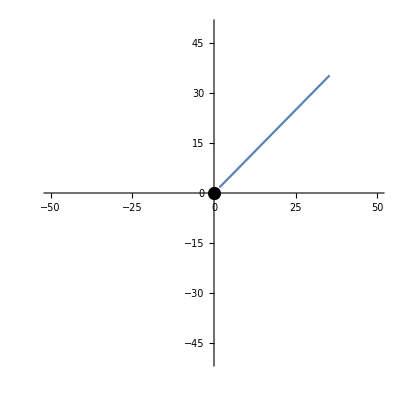

```mathematica
(*
Produces a list of coordinates displayed below in this fashion: (φ,r).
The same list is then used in a polar plot with connected points.
Epilog->Disk[{0,0},rs] superimposes a black sphere of Schwarzschild radius as reference.
*)
coords=Transpose[{Flatten[Table[φ[s]/.sol, {s, 0, steps}]], Flatten[Table[r[s]/.sol, {s, 0, steps}]]}]; (*remove ; to see coords list*)
ListPolarPlot[coords,PlotRange->All,Epilog->Disk[{0,0},rs],Joined->True]
```

Animated plot

```mathematica
(*
Animates the polar plot without connected points. This allows you to see the relative speed of the orbit.
Calculating the instantaneous speed wouldn't even be hard. Just take r'[s] if you're curious.
The animation is set to display 50 dots/second (DefaultDuration-> steps/50).
*)
Animate[
ListPolarPlot[
Transpose[{Flatten[Table[φ[s]/.sol,{s, 0, frames}]],Flatten[Table[r[s]/.sol,{s, 0, frames}]]}],
PlotRange->All,
Epilog->Disk[{0,0},rs]
],
{frames, 0, steps},
AnimationRunning->False,
DefaultDuration-> steps/50
]
```